```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls",
"load_takahashi_data.wl"
};
```

```mathematica
figureNumberRepairShort="Fig_4";
figureNumberRepairLong=figureNumberRepairShort<>"_repair_dark_vs_light";
```

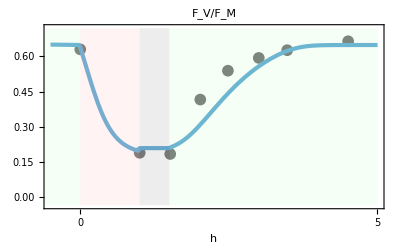
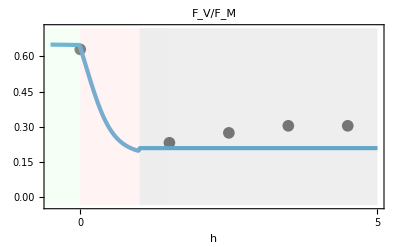
-Graphics--Graphics-Light
μmol quanta m^-2s^-1
40 | RGBColor[0.88, 1, 0.88]
2000 | RGBColor[1, 0.85, 0.85]
0 | RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778]

```mathematica
(*for numerical stability: a function that turns a sudden up down ramp in a continuous function, with a small ramp up-down time*)
makeRampedPiecewise[data_List,rampTime_]:=Module[{vals=data[[All,1]],ends=data[[All,2]],n=Length[data],segments},segments=Table[Module[{v1=vals[[i]],v2=vals[[i+1]],tFlatEnd=ends[[i]],(*flat part ends*)tRampEnd=ends[[i+1]],(*ramp finishes at next segment end*)tRampStart},tRampStart=tRampEnd-rampTime;
{(*flat part*){v1,t<tRampStart},(*ramp part*){v1+(v2-v1) ((t-tRampStart)/rampTime),tRampStart<=t<tRampEnd}}],{i,1,n-1}];
segments=Flatten[segments,1];
(*Final value stays constant from the last endpoint onward*)AppendTo[segments,{Last[vals],t>=Last[ends]}];
Piecewise[segments]];
(*ramp up down time*)
rampTime=10;
(*define parameters (including light)*)
parsRepairByLight[repairLight_]:=Join[{
L->makeRampedPiecewise[{{40,-24 3600},{2000,0},{0,3600},{repairLight,1.5 3600}},100],
tmin->-24 3600,
tmax->24 3600
},
pars[4]
];
(*the lights at the end of the experiment*)
repairLights={0,40};
(*load takahashi data*)
dat["Repair"][40]=DeleteDuplicates@Normal@Select[data["Fig3B"],#"temp"==25.&][All,{3600(#["h"]+1.5)&,#["Fv/Fm"]&}];
dat["Repair"][0]=DeleteDuplicates@Normal@Select[data["FigS3"],#"temp"==25.&][All,{3600(#["h"]+1.5)&,#["Fv/Fm"]&}];
(*styles*)
lightShadingColors={0->Lighter@Lighter@Gray,40->LightGreen,2000->LightRed};
timesRepairPlots={-.5 3600,5 3600};
plotRepairByLight=Table[
Show[{ListPlot[dat["Repair"][repairLight],Joined->False,PlotMarkers->plotMarkers,PlotStyle->{Darker@Gray,Dashed,thickness},imageSizePadding[ImagePaddingXunits],FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks[[1;;-1;;1]],None}},
FrameLabel->{{None,None},{"h",None}},PlotRange->{timesRepairPlots,{FvFmMinPlot,FvFmMaxPlot}},Evaluate@style,PlotLabel->"F_V/F_M"],
plotSimulation[FvFm,parsRepairByLight[repairLight],timesRepairPlots,{Evaluate@imageSizePadding[ImagePaddingUnits],PlotRange->Full,FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks,None}}
}]},PlotRange->{{-.5,5}3600,{FvFmMinPlot,FvFmMaxPlot}},

Epilog->{
{40/.lightShadingColors,Opacity[0.3],Rectangle[{-1 3600,FvFmMinPlot},{0 3600,FvFmMaxPlot}]},
{2000/.lightShadingColors,Opacity[0.3],Rectangle[{0 3600,FvFmMinPlot},{1 3600,FvFmMaxPlot}]},
{0/.lightShadingColors,Opacity[0.3],Rectangle[{1 3600,FvFmMinPlot},{1.5 3600,FvFmMaxPlot}]},
{repairLight/.lightShadingColors,Opacity[0.289],Rectangle[{1.501 3600,FvFmMinPlot},{5 3600,FvFmMaxPlot}]},
Nothing
}],{repairLight,Reverse@repairLights}];
legendRepairByLight=Column[{Style["Light",FontFamily->font,14],Style[L/.units,FontFamily->font,14],Grid[Table[{Style[light,FontFamily->font,14],light/.lightShadingColors},{light,{40,2000,0}}],Alignment->Right]},Alignment->Center];
(*make plot*)
(Export[NotebookDirectory[]<>figureNumberRepairLong<>"/"<>figureNumberRepairShort<>".pdf",#];#)&@Row[plotRepairByLight~Join~{Column[{legendRepairByLight,Spacer[{20,20}]}]}]
```

```mathematica
Table[(Export[NotebookDirectory[]<>figureNumberRepairLong<>"/"<>figureNumberRepairShort<>"_SI_light="<>ToString[repairLight]<>".pdf",#];#)&@fullSimulationPanel[parsRepairByLight[repairLight],timesRepairPlots,{FrameTicks->{{autoTicks,None},{{0}~Join~hourTicks[[1;;-1;;1]],None}}},{(FrameLabel->{{#/.units,None},{"h",None}})}&], {repairLight,repairLights}];
```